```mathematica
Quit[]
```

```mathematica
M = {{1,Subscript[x, 1],Subscript[x, 1]^2},{1,Subscript[x, 2],Subscript[x, 2]^2},{1,Subscript[x, 3],Subscript[x, 3]^2}}
```

{{1,x_1,x_1^2},{1,x_2,x_2^2},{1,x_3,x_3^2}}

```mathematica
Inverse[M]
```

{{(-x_2^2 x_3+x_2 x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(x_1^2 x_3-x_1 x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(-x_1^2 x_2+x_1 x_2^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)},{(x_2^2-x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(-x_1^2+x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(x_1^2-x_2^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)},{(-x_2+x_3)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(x_1-x_3)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(-x_1+x_2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)}}

```mathematica
y  = {1,x,x^2}
```

{1,x,x^2}

```mathematica
Ne = y.Inverse[M]
```

{(x^2 (-x_2+x_3))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(x (x_2^2-x_3^2))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(-x_2^2 x_3+x_2 x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(x^2 (x_1-x_3))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(x (-x_1^2+x_3^2))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(x_1^2 x_3-x_1 x_3^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2),(x^2 (-x_1+x_2))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(x (x_1^2-x_2^2))/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)+(-x_1^2 x_2+x_1 x_2^2)/(-x_1^2 x_2+x_1 x_2^2+x_1^2 x_3-x_2^2 x_3-x_1 x_3^2+x_2 x_3^2)}

```mathematica
(*assuming*)
Subscript[x, 1]= 0
Subscript[x, 2]= 1
Subscript[x, 3]= 2
```

0

1

2

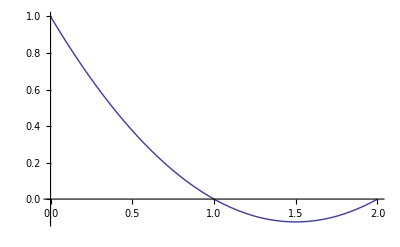

```mathematica
Plot[(z^2 (-Subscript[x, 2]+Subscript[x, 3]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z(Subscript[x, 2]^2-Subscript[x, 3]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(-Subscript[x, 2]^2 Subscript[x, 3]+Subscript[x, 2] Subscript[x, 3]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2),{z,0,2}]
```

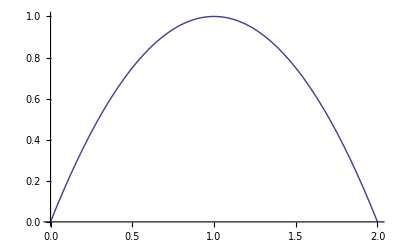

```mathematica
Plot[(z^2 (Subscript[x, 1]-Subscript[x, 3]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z (-Subscript[x, 1]^2+Subscript[x, 3]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2),{z,0,2}]
```

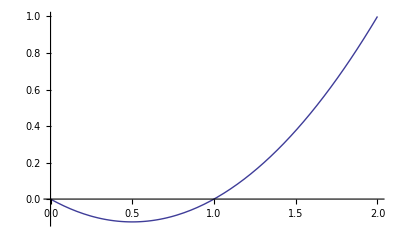

```mathematica
Plot[(z^2 (-Subscript[x, 1]+Subscript[x, 2]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z (Subscript[x, 1]^2-Subscript[x, 2]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2),{z,0,2}]
```

```mathematica
Simplify[D[{(z^2 (-Subscript[x, 2]+Subscript[x, 3]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z (Subscript[x, 2]^2-Subscript[x, 3]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(-Subscript[x, 2]^2 Subscript[x, 3]+Subscript[x, 2] Subscript[x, 3]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2),(z^2 (Subscript[x, 1]-Subscript[x, 3]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z (-Subscript[x, 1]^2+Subscript[x, 3]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2),(z^2 (-Subscript[x, 1]+Subscript[x, 2]))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(z (Subscript[x, 1]^2-Subscript[x, 2]^2))/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)+(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2)/(-Subscript[x, 1]^2 Subscript[x, 2]+Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1]^2 Subscript[x, 3]-Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 3]^2+Subscript[x, 2] Subscript[x, 3]^2)},z]]
```

{-(-2 z+x_2+x_3)/((x_1-x_2) (x_1-x_3)),(-2 z+x_1+x_3)/((x_1-x_2) (x_2-x_3)),(-2 z+x_1+x_2)/((x_1-x_3) (-x_2+x_3))}